# Лабораторная работа 11. Компьютерные модели аналитической геометрии. Геометрические объекты “Точка на плоскости”, “Вектор на плоскости”

Выполнила студентка ММФ БГУ
 1 к, 5 гр. Шклярик В.С.
 17 ноября 2021

```mathematica
ClearAll[kmPoint];
kmPoint[coord:{_,_}]:=kmPoint[km,"",coord];
kmPoint[id_String,coord:{_,_}]:=kmPoint[km,id,coord];
kmPoint[{ϕ_,ρ_},"pol"]:=kmPoint[km,"",{ρ Cos[ϕ],ρ Sin[ϕ]}];
kmPoint[id_String,{ϕ_,ρ_},"pol"]:=kmPoint[km,id,{ρ Cos[ϕ],ρ Sin[ϕ]}];
kmPoint[km,id_String,___]["id"]:=If[id=="","Точка",id];
kmPoint[km,id_String,coord_List,___]["coord"]:=coord;
NamedQ[kmPoint[km,id_String,___]]^:=id≠"";
ClearAll[kmGraphics2D];
kmGraphics2D[gp_List,opts___]:=Graphics[Point/@(#["coord"]&/@gp),opts];
```

## Задание 1

```mathematica
{P1,P2,P3}=kmPoint/@{{-1,0},{5,3},{-2,2}}
```

{kmPoint[km,,{-1,0}],kmPoint[km,,{5,3}],kmPoint[km,,{-2,2}]}

```mathematica
ClearAll[kmPointShow];
kmPointShow[gp_List,color_:Black,opts___]:=Graphics[{ReplaceAll[gp,P_kmPoint:>{color,AbsolutePointSize[5],Tooltip[Point@P@"coord",{P/@{"id","coord"},TreeForm@P}]}]},opts];
```

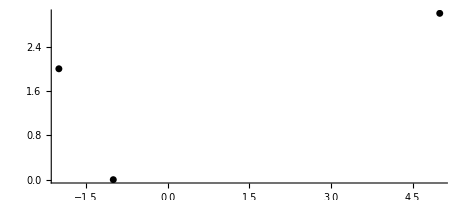

```mathematica
kmPointShow[{P1,P2,P3},,Axes->True]
```

### Задание 2.1

```mathematica
ℳ=kmPoint["ℳ",{(7 π)/4,2},"pol"]
```

kmPoint[km,ℳ,{√2,-√2}]

```mathematica
ℳ["coord"]
```

{√2,-√2}

```mathematica
ℳ["id"]
```

ℳ

```mathematica
kmPointShow[{ℳ},Green]
```

-Graphics-

### Задание 2.2

```mathematica
ClearAll[dist]
```

```mathematica
M=kmPoint["M",{π/4,2},"pol"]
Ν=kmPoint["Ν",{(3 π)/4,6},"pol"]
```

kmPoint[km,M,{√2,√2}]

kmPoint[km,Ν,{-3 √2,3 √2}]

```mathematica
dist[P1_kmPoint,P2_kmPoint]:=√(#.#)&[P2["coord"]-P1["coord"]]
```

```mathematica
dist[P1,P2]
```

3 √5

```mathematica
𝒪=kmPoint[km,"𝒪",{0,0}]
```

kmPoint[km,𝒪,{0,0}]

```mathematica
dist[M,𝒪]
```

2

```mathematica
dist[𝒪,Ν]
```

6

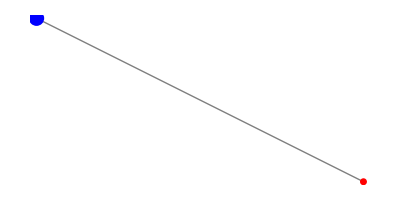

```mathematica
Show[Graphics[{Gray,Tooltip[Line[#["coord"]&/@{M,Ν}],dist[M,Ν]]}],kmPointShow[{M},Red],kmPointShow[{Ν},Blue]/.AbsolutePointSize[5]:>AbsolutePointSize[11]]
```

### Задание 2.3

```mathematica
kmPoint[id_String,A_,B_,λ_]:=kmPoint[id,((A["coord"]+λ B["coord"])/(1+λ))⟦#⟧&/@{1,2}];
```

```mathematica
kmPoint["C",M,Ν,1/2]
```

kmPoint[km,C,{2/3 (-3/(√2)+√2),2/3 (3/(√2)+√2)}]

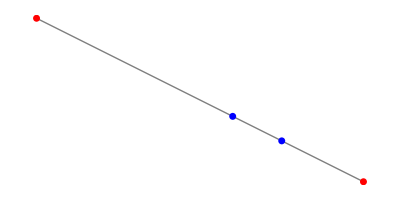

```mathematica
Show[Graphics[{Gray,Line[#["coord"]&/@{M,Ν}]}],kmPointShow[{M,Ν},Red],kmPointShow[{kmPoint["T",M,Ν,1/3],kmPoint["L",M,Ν,2/3]},Blue]]
```

```mathematica
Point[#["coord"]&/@{M,Ν}]
```

Point[{{√2,√2},{-3 √2,3 √2}}]

### Задание 2.4

```mathematica
Y=kmPoint["Y",{(7 π)/4,4},"pol"]
```

kmPoint[km,Y,{2 √2,-2 √2}]

Функция kmPoint[triangle:{A_,B_,𝒞_},”bisAcrossBC”] по заданному списку координат трех точек строит объект “точка на плоскости” для представления

```mathematica
kmPoint[triangle:{A_,B_,𝒞_},"bisAcrossBC"]:=kmPoint[StringJoin["bisAcross",#["id"]&/@{B,𝒞}],𝒞,B,dist[A,𝒞]/dist[A,B]];
```

```mathematica
kmPoint[{M,Ν,Y},"bisAcrossBC"]
```

kmPoint[km,bisAcrossΝY,{(-3+2 √2)/(1+1/(√2)),(3-2 √2)/(1+1/(√2))}]

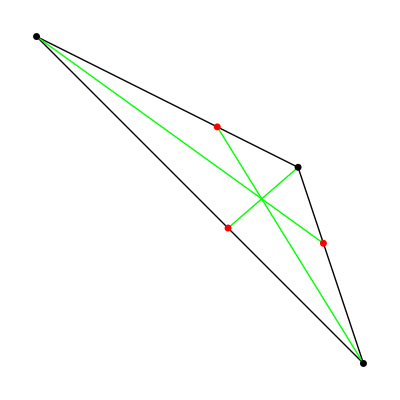

```mathematica
Module[{k1=kmPoint[{M,Ν,Y},"bisAcrossBC"],k2=kmPoint[{Ν,Y,M},"bisAcrossBC"],k3=kmPoint[{Y,M,Ν},"bisAcrossBC"]},Show[Graphics[{Line[#["coord"]&/@{M,Ν,Y,M}]}],Graphics[{Green,Line@@{MapThread[List,{#["coord"]&/@{M,Ν,Y},
#["coord"]&/@{k1,k2,k3}}]}}],kmPointShow[{k1,k2,k3},Red],kmPointShow[{M,Ν,Y}]]]
```

```mathematica
polygonVecrtices[n_Integer,r_]:=Table[kmPoint["vertex",{ (2 π)/n*i,r},"pol"],{i,1,n,1}]/;n>2
```

```mathematica
polygonVecrtices[6,6]
```

{kmPoint[km,vertex,{3,3 √3}],kmPoint[km,vertex,{-3,3 √3}],kmPoint[km,vertex,{-6,0}],kmPoint[km,vertex,{-3,-3 √3}],kmPoint[km,vertex,{3,-3 √3}],kmPoint[km,vertex,{6,0}]}

```mathematica
polygonShow[n_,r_,opts___]:=Module[{poly=polygonVecrtices[n,r]},Show[Graphics[Circle[𝒪["coord"],r]],Graphics[{Orange,Line[#["coord"]&/@Append[poly,poly//First]]}],kmPointShow[poly,Red],opts]]
```

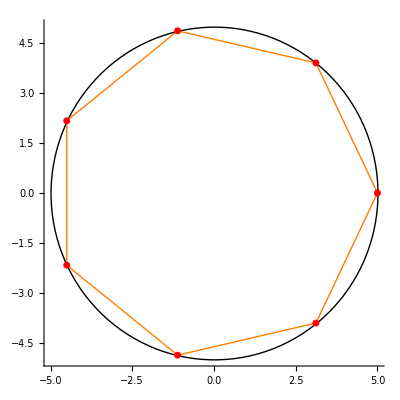

```mathematica
polygonShow[7,5,Axes->True]
```

## Задание 3

### Задание 3.1

kmVector[km, id_String, coord_List]

### Задание 3.2

Булева функция NamedQ возвращает значение True в случае, если 
объект «вектор» является именованным объектом, и значение False в 
противном случае.

```mathematica
NamedQ[kmVector[km,id_String,___]]^:=id≠"";
```

```mathematica
NamedQ[p1]//Trace
```

{{p1,kmPoint[km,B,{-2,3}]},NamedQ[kmPoint[km,B,{-2,3}]],B≠,True}

```mathematica
NamedQ[kmVector[km,"AB",{-5,-1}]]
```

True

```mathematica
NamedQ[kmVector[km,"",{95,1}]]//Trace
```

{NamedQ[kmVector[km,,{95,1}]],≠,False}

### Задание 3.3 - 3.4

Конструктор

```mathematica
kmVector[id_String,coord_List]:=kmVector[km, id,coord ]; (*базовый*)
```

```mathematica
kmVector[coord_List]:=kmVector["",coord];
```

```mathematica
kmVector[id_String,p0_kmPoint,p1_kmPoint]:=kmVector[id,p1["coord"]-p0["coord"]];
```

```mathematica
{p0,p1}=MapThread[kmPoint[#1,#2]&,{{"A","B"},{{3,4},{-2,3}}}]
```

{kmPoint[km,A,{3,4}],kmPoint[km,B,{-2,3}]}

```mathematica
kmVector[p0_kmPoint,p1_kmPoint]:=kmVector[If[And@@NamedQ/@{p0,p1},StringJoin[p0@"id",p1@"id"],""],p0,p1];
```

```mathematica
kmVector[p0,p1]
```

kmVector[km,AB,{-5,-1}]

### Задание 3.5 - 3.6

```mathematica
kmVector[id_String,ort:{_,_},length_]:=kmVector[id,ort*length];
```

```mathematica
kmVector[ort:{_,_},length_]:=kmVector["",ort*length];
```

### Задание 3.7 - 3.8

```mathematica
kmVector[km,id_String,___]["id"]:=If[id=="","Вектор",id];
```

```mathematica
kmVector[km,id_String,coord_List,___]["coord"]:=coord;
```

### Задание 3.9

```mathematica
kmVector[km,id_String,coord_List,___]["length"]:=√(#.#)&[kmVector[id,coord]["coord"]]
```

```mathematica
kmVector[p0,p1]["length"]
```

√26

### Задание 3.10

```mathematica
kmVector[km,id_String,coord_List,___]["ort"]:=(kmVector[id,coord]["coord"])/(kmVector[id,coord]["length"]);
```

### Тесты

```mathematica
kmVector[p0,p1]["ort"]
```

{-5/(√26),-1/(√26)}

```mathematica
MY=kmVector["MY",M,Y]
```

kmVector[km,MY,{√2,-3 √2}]

```mathematica
MY["ort"]
```

{1/(√10),-3/(√10)}

```mathematica
MY["length"]
```

2 √5

```mathematica
NamedQ[MY]
```

True

```mathematica
kmVector["vec",{2/(√5),-1/(√5)},4 √13]
```

kmVector[km,vec,{8 √(13/5),-4 √(13/5)}]

```mathematica
kmVector[{2,8},{-3,-5}]
```

kmVector[km,,{-6,-40}]

```mathematica
kmVector[km,"",{-6,-40}]["id"]
```

Вектор

```mathematica
NamedQ[kmVector[km,id_String,___]]^:=id≠"";
kmVector[id_String,coord_List]:=kmVector[km, id,coord ];
kmVector[coord_List]:=kmVector["",coord];
kmVector[id_String,p0_kmPoint,p1_kmPoint]:=kmVector[id,p1["coord"]-p0["coord"]];
kmVector[p0_kmPoint,p1_kmPoint]:=kmVector[If[And@@NamedQ/@{p0,p1},StringJoin[p0@"id",p1@"id"],""],p0,p1];
kmVector[id_String,ort:{_,_},length_]:=kmVector[id,ort*length];
kmVector[ort:{_,_},length_]:=kmVector["",ort*length];
kmVector[km,id_String,___]["id"]:=If[id=="","Вектор",id];
kmVector[km,id_String,coord_List,___]["coord"]:=coord;
kmVector[km,id_String,coord_List,___]["length"]:=√(#.#)&[kmVector[id,coord]["coord"]];
kmVector[km,id_String,coord_List,___]["ort"]:=(kmVector[id,coord]["coord"])/(kmVector[id,coord]["length"]);
```